```mathematica
r={a Cos[#],b Sin[#],0}&
v=L/(μ ro) {-Sin[#],e+Cos[#],0}&
Rmat=EulerMatrix[{65,135,-40} π/180,{3,1,3}]//N;
```

{a Cos[#1],b Sin[#1],0}&

(L {-Sin[#1],e+Cos[#1],0})/(μ ro)&

```mathematica
(L {-Sin[#1],e+Cos[#1]})/(μ ro)&
```

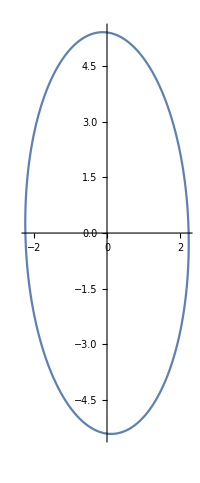

```mathematica
ParametricPlot[Rmat.r[x].{{1,0},{0,1},{0,0}},{x,0,2π}]
```

```mathematica
Rmat1=RotationMatrix[ArcTan[-l/m],{0,0,1}].EulerMatrix[{ArcTan[l/m],ArcCos[Sqrt[1-l^2-m^2]],0},{3,1,3}];
```

```mathematica
FullSimplify[Rmat1.r[x]]
```

{a Cos[x],b √(1-l^2-m^2) Sin[x],b √(l^2+m^2) Sin[x]}

```mathematica
Rmat2=EulerMatrix[{ArcTan[l/m],ArcCos[Sqrt[1-l^2-m^2]],-ArcTan[-l/m]},{3,1,3}];
```

```mathematica
FullSimplify[Rmat2.r[x]]
```

{(a (m^2-l^2 √(1-l^2-m^2)) Cos[x]-b l m (1+√(1-l^2-m^2)) Sin[x])/(l^2+m^2),(a l m (1+√(1-l^2-m^2)) Cos[x]+b (-l^2+m^2 √(1-l^2-m^2)) Sin[x])/(l^2+m^2),(√(1+l^2/m^2) m (a l Cos[x]+b m Sin[x]))/(√(l^2+m^2))}